```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/fluc_T/fluctuations_T/highorder_2p1/input_h/finitemub_v4/phase/phase_boundaryTc230a0p5_v2

```mathematica
mf=Table[Transpose[Import["./TemB"<>ToString[i]<>"/BUFFER/MF.DAT"]][[1]],{i,1,37}];
intdmfdt=Table[-D[Interpolation[mf[[i]]][x],x],{i,1,37}];
mub=Flatten[{Table[i*15,{i,1,37}]}]
Tpc=Table[FindMaximum[{intdmfdt[[i]],90<x<200},{x,160}][[2]][[1]][[2]],{i,1,37}];
peak=Table[FindMaximum[{intdmfdt[[i]],90<x<200},{x,160}][[1]],{i,1,37}];
Tpcup80=Table[FindRoot[intdmfdt[[i]]==peak[[i]]*0.8,{x,Tpc[[i]]+5}][[1]][[2]],{i,1,37}];
Tpcdown80=Table[FindRoot[intdmfdt[[i]]==peak[[i]]*0.8,{x,Tpc[[i]]-5}][[1]][[2]],{i,1,37}];
fitTpc=FindFit[Transpose[{mub,Tpc}],a+b x^2+c x^4(*+d x^6*),{a,b,c},x];
fitTpcup=FindFit[Transpose[{mub,Tpcup80}],a+b x^2+c x^4,{a,b,c},x];
fitTpcdown=FindFit[Transpose[{mub,Tpcdown80}],a+b x^2+c x^4,{a,b,c},x];
```

{15,30,45,60,75,90,105,120,135,150,165,180,195,210,225,240,255,270,285,300,315,330,345,360,375,390,405,420,435,450,465,480,495,510,525,540,555}

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

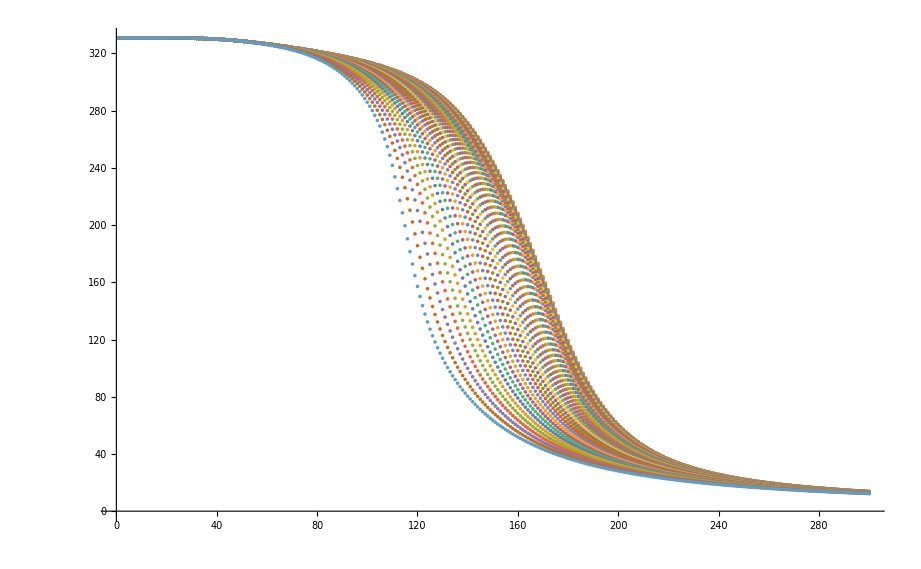

```mathematica
ListPlot[mf]
```

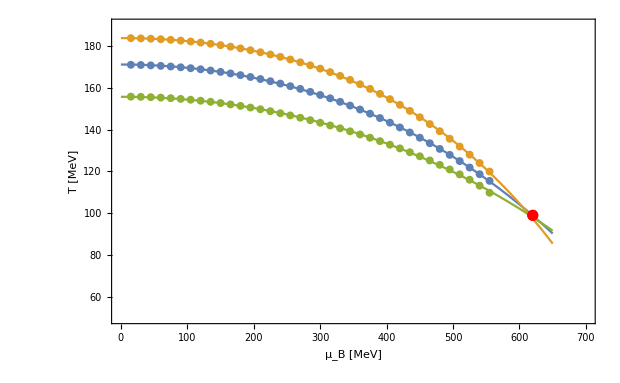

./parav3.pdf

```mathematica
Show[ListPlot[{Transpose[{mub,Tpc}],Transpose[{mub,Tpcup80}],Transpose[{mub,Tpcdown80}]},PlotRange->{{0,700},{50,190}}],Plot[{a+b x^2+c x^4/.fitTpc,a+b x^2+c x^4/.fitTpcup,a+b x^2+c x^4/.fitTpcdown},{x,0,650}],ListPlot[{{620,99}},PlotStyle->Red],Frame->True,FrameLabel->{Style["μ_B [MeV]",15,Black],Style["T [MeV]",15,Black]}]
Export["./parav3.pdf",%]
```

```mathematica
Export["phaseboundary.dat",Transpose[{mub,Tpc}]]
```

phaseboundary.dat

```mathematica
mubfo[sqrts_]:=1307.5/(1+0.288 sqrts);
sqrts[muB_]:=-(1.7361111111111112 (-2615.+2. muB))/muB;
Tfo[muB_]:=158.4/(1+Exp[2.60-Log[(1307.5/muB-1)/0.288]/0.45]);
STARFitI=Transpose[{Flatten[Import["./freezeout/mub.dat"]],Flatten[Import["./freezeout/STARFitI.dat"]]}];
STARFitII=Transpose[{Flatten[Import["./freezeout/mub.dat"]],Flatten[Import["./freezeout/STARFitII.dat"]]}];
TI=Table[Interpolation[STARFitI][mub[[i]]],{i,2,Length[mub]}];
TII=Table[Interpolation[STARFitII][mub[[i]]],{i,2,Length[mub]}];
```

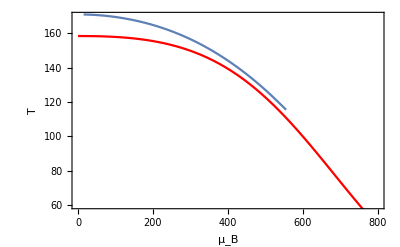

./phase.pdf

```mathematica
Freezeoutplot=Plot[Tfo[x],{x,0,800},PlotStyle->Red,PlotLegends->Placed[{"Freeze-out Andronic et al."},{Right,Top}]];
Phase=ListLinePlot[{Transpose[{mub,Tpc}]},PlotLegends->Placed[{"Phase Boundary"},{Right,Top}]];
Show[Freezeoutplot,Phase,PlotRange->{All,{60,170}},Frame->True,FrameLabel->{Style["μ_B",15,Black],Style["T",15,Black]}]
Export["./phase.pdf",%]
```